```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/akcays/Desktop/BNS_GRB_work/Sarps_work

# SETTING UP

## STRAIN DATA

### OLD DATA for ENDPOINTS

```mathematica
ALIGODesigndata={{10^5,10^4,100,32,20,8,5,2.35,1,0.6,0.4,0.3,0.25,0.3,0.8,3}*10^-23,{6,7,9,9.7,10,11.89,14,20,30,40,60,200,300,400,900,1200}};
ASDvFreqData=Table[{ALIGODesigndata[[2,j]],ALIGODesigndata[[1,j]]},{j,1,Length[ALIGODesigndata[[1]]]}];
ExtraETCData={{1.1388108937271446,9.609459526468317 10^-22},{1.1529964151058092,7.8114842961191475 10^-22},{1.1892381077160423,5.957808026448449 10^-22},{1.2190499622963578,4.999907130470519 10^-22}};
NewETBdata={{1.167358637478373,8.944521110882274 10^-22},{1.1892381077160423,7.446845066646906 10^-22},{1.2266189715032598,5.863623678813286 10^-22},{1.2651748135966814,4.96022903404055 10^-22}};
```

### Jocelyn Read’s Realistic BNS Inspiral DATA

```mathematica
ReadBNSData=Import["BNS_data_Read.csv","Data"];
RealisticBNSData=Sort[ReadBNSData];
```

### A-LIGO DESIGN, ET-B, ET-C DATA

```mathematica
TextSize=22;
ALIGO2020Data=Join[{ASDvFreqData[[1]]},{ASDvFreqData[[3]]},Sort[Import["ALIGO2020.csv","Data"]]];
ETBData=Join[NewETBdata,Drop[Sort[Import["ET_B.csv","Data"]],{1,5}]](*Sort[Import["ET_B.csv","Data"]]*);
ETCData=Join[ExtraETCData,Drop[Sort[Import["ET_C.csv","Data"]],{1}]](*Sort[Import["ET_C.csv","Data"]]*);
```

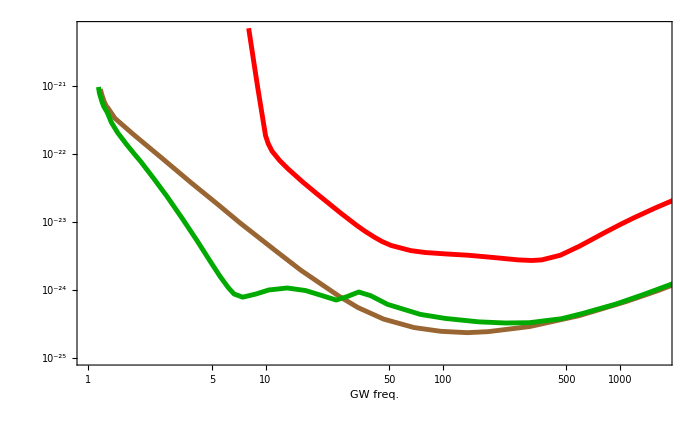

```mathematica
IFOASDs=ListLogLogPlot[{ALIGO2020Data,ETBData,ETCData},PlotRange->{{1,1700},{10^-25,7 10^-21}},Joined->True,PlotStyle->{{Thickness[0.005],Red},{Thickness[0.005],Brown},{Thickness[0.005],Darker[Green]}},AxesLabel->{"GW freq.",None},ImageSize->700,Frame->True,FrameStyle->Thick,FrameTicksStyle->24,Epilog->Inset[Framed[Column[{LineLegend[{Directive[{Thickness[0.0125],Red}],{Thickness[0.0125],Brown},{Thickness[0.0125],Darker[Green]}},{Style["New A-LIGO2020",TextSize],Style["New ET-B",TextSize],Style["ET-C",TextSize]}]}],RoundingRadius->5,FrameStyle->Directive[Black,AbsoluteThickness[4]],Background->White],Scaled[{0.75,0.75}]]]
(*Export["Figures/All_IFO_strains.pdf",IFOASDs]*)
```

## INTERPOLATED STRAIN DATA: S_noise(f_GW)

### INTERPOLATE ASD DATA: use low InterpOrd to avoid waviness in the fits

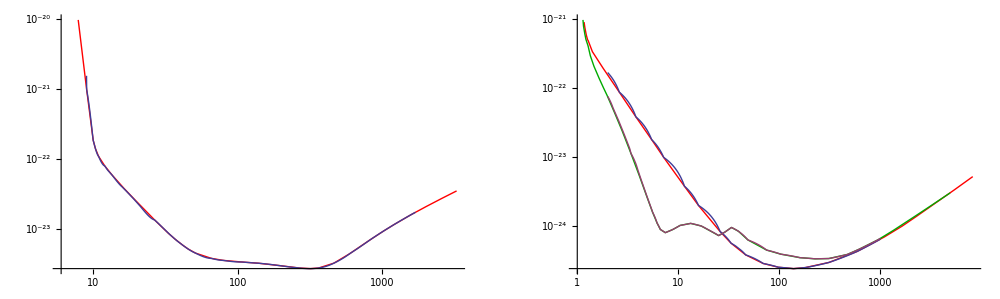

```mathematica
Snoise={Interpolation[ALIGO2020Data,InterpolationOrder->2],
Interpolation[ETBData,InterpolationOrder->1],Interpolation[ETCData,InterpolationOrder->1]};
GraphicsRow[{Show[ListLogLogPlot[ALIGO2020Data,Joined->True,PlotStyle->Red],LogLogPlot[Snoise[[1]][x],{x,6,1700}]],Show[ListLogLogPlot[{ETBData,ETCData},Joined->True,PlotStyle->{Red,Darker[Green]}],LogLogPlot[{Snoise[[2]][x],Snoise[[3]][x]},{x,2,1000}]]},ImageSize->1000]
```

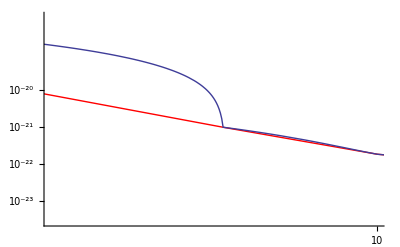

```mathematica
Show[ListLogLogPlot[ALIGO2020Data,Joined->True,PlotStyle->Red],LogLogPlot[Snoise[[1]][x],{x,6,100}],PlotRange->{{Log[8],Log[10]},Automatic}]
```

## Preliminaries

```mathematica
Clear[x,h]
```

```mathematica
A=π^(-2/3)√(5/24);
X=(G M Ω/c^3)^(2/3);
Msun=1.989*10^30;
clight=299792458;
Ggrav=6.67*10^-11;
ν=1/4;
mu= (1.4 Msun)^2/Mtot
Mc=ν^(3/5)M;
fISCO=c^3/(6^(3/2)π G M);
AngAveFact=1/Pi Integrate[(1+Cos[i]^2)/2,{i,0,Pi}];
Mpc=10^6*360/(2π)*3600*149597870700.;
GWfreqIsco=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},fISCO]
fISCOGW170817=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},fISCO]
Mtot=2.8 Msun;
```

(7.754×10^60)/Mtot

1570.97

1605.37

```mathematica
rdim=(400/(1/π^2 clight^6/(Ggrav*2.7*Msun)^2))^(-1/3)
```

112.747

```mathematica
rdim^(-3/2)/π
```

0.000265884

```mathematica
(Ggrav*2.7)/π^2 Msun/((rdim*Ggrav 2.7 Msun/clight^2)^3)
```

400.

```mathematica
Mc/.M->2.8`4
```

1.219

## AVERAGING of the L-TOPOLOGY ANTENNA PATTERNS

```mathematica
InclinationAv=1/2 Integrate[(((1+Cos[i]^2)/2)^2+Cos[i]^2)Sin[i],{i,0,-Pi,Pi}]
```

4/5

```mathematica
Fplus=1/2(1+Cos[θ]^2)Cos[2ϕ]Cos[2ψ]-Cos[θ]Sin[2ϕ]Sin[2ψ];
Fx=1/2(1+Cos[θ]^2)Cos[2ϕ]Sin[2ψ]+Cos[θ]Sin[2ϕ]Cos[2ψ];
```

```mathematica
Fplus/.ψ->0/.ϕ->0/.θ->0
```

1

```mathematica
(*Average over θ,ϕ,ψ*)
1/(8 Pi^2)Integrate[Fplus^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
1/(8 Pi^2)Integrate[Fx^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
LowAv=√(1/5 InclinationAv)
```

1/5

1/5

2/5

```mathematica
(*Set ψ=0, average over θ,ϕ*)
1/(4Pi)Integrate[Fplus^2*Sin[θ]/.ψ->0,{θ,0,Pi},{ϕ,0,2π}]
1/(4Pi)Integrate[Fx^2*Sin[θ]/.ψ->0,{θ,0,Pi},{ϕ,0,2π}]
MedAv=√(7/30+1/6)
```

7/30

1/6

√(2/5)

## Inspiral time, accumulated phase: 0PN to 3.5PN expressions

```mathematica
Tinsp0PN[f0_,Mch_]=5/(256 π^(8/3))  (c^3/(G Mch))^(5/3) f0^(-8/3)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Phi0PN[f0_,Mch_,M_]=2 (5 G Mch/c^3)^(-5/8) Tinsp0PN[f0,Mch]^(5/8)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Ncycles0PN[f0_,Mch_,M_]=1/(32 π^(8/3)) (G Mch/c^3)^(-5/3) (f0^(-5/3)-fISCO^(-5/3))/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;

(*2PN expressions from Section 5.6.4 of Maggiore's Book*)

τ0[f_,M_]:=5/(256 ν f π) (π G M/c^3 f)^(-5/3)/.G->6.67*10^-11/.c->clight;
τ1[f_,M_]:=5/(192 ν f π) (π G M/c^3 f)^-1 (743/336+11/4 ν)/.G->6.67*10^-11/.c->clight;
τ15[f_,M_]:=1/(8 ν f) (π G M/c^3 f)^(-2/3)/.G->6.67*10^-11/.c->clight;
τ2[f_,M_]:=5/(128 ν f π) (π G M/c^3 f)^(-1/3) (3058673/1016064+5429/1008 ν+617/144 ν^2)/.G->6.67*10^-11/.c->clight;

Tinsp2PN[f_,fin_,M_]:=τ0[fin,M] (1-(f/fin)^(-8/3))+τ1[fin,M] (1-(f/fin)^-2)-τ15[fin,M] (1-(f/fin)^(-5/3))+τ2[fin,M] (1-(f/fin)^(-4/3));
Phi2PN[f_,fin_,M_]:=16 π/5 fin (τ0[fin,M] (1-(f/fin)^(-5/3))+5/4 τ1[fin,M] (1-(f/fin)^-1)-25/16 τ15[fin,M] (1-(f/fin)^(-2/3))+5/2 τ2[fin,M] (1-(f/fin)^(-1/3)));
```

### 2+ PN from Blanchet’s Review Article

```mathematica
(* 3.5 PN non-spinning binary phase *)
K=SeriesCoefficient[X/.Ω-> π f,{f,0,2/3}];
Xvar[f_]=K f^(2/3);
(* x0 is an integration constant *)
phi[x_,x0_]=-x^(-5/2)/(32ν)(1+(3715/1008+55/12 ν)x-10 π x^(3/2)+(15293365/1016064+27145/1008 ν+3085/144 ν^2)x^2+(38645/1344-65/16 ν)π x^(5/2)Log[x/x0]+(12348611926451/18776862720-160/3 π^2-1712/21 EulerGamma-856/21 Log[16x]+(-15737765635/12192768+2255/48 π^2)ν+76055/6912 ν^2-127825/5184 ν^3)x^3+(77096675/2032128+378515/12096 ν-74045/6048 ν^2)π x^(7/2));
```

```mathematica
(* Accumulated phase from x1 to x2 = Φ[x1] - Φ[x2] *)
(*PhiAcc[x1_,x2_]=FullSimplify[phi[x1,x0]-phi[x2,x0]]/.Log[x1/x0]-Log[x2/x0]->Log[x1/x2];*)
```

### SOLVING x(Θ) = x(f=30Hz) for Θ gives us inspiral time

```mathematica
Clear[T]
(* Θ is a rescaled time variable where Δt = Subscript[t, coal]- t *)
Θ=ν c^3/(G M)(Δt)/5;
xoft[T_]=(1/4)T^(-1/4)(1+(743/4032+11/48 ν)T^(-1/4)-1/5 π T^(-3/8)+(19583/254016+24401/193536 ν+31/288 ν^2)T^(-1/2)+(-11891/53760+109/1920 ν)π T^(-5/8)+(-10052469856691/6008596070400+1/6 π^2+107/420 EulerGamma-107/3360 Log[T/256]+(3147553127/780337152-451/3072 π^2)ν-15211/442368 ν^2+25565/331776 ν^3)T^(-3/4)+(-113868647/433520640-31821/143360 ν+294941/3870720 ν^2)π T^(-7/8));
```

# EINSTEIN TELESCOPE

## RE-AVERAGING of the ANTENNA PATTERNS for the EINSTEIN TELESCOPE: 1201.3563

### ANTENNA PATTERN FUNCTIONS: √3/2 times L-shaped F_(+,x) and rotated by 2π/3

```mathematica
Fplus1=(√3)/2 Fplus;
Fx1=(√3)/2 Fx;
Fplus2=(√3)/2 FullSimplify[Fplus/.ϕ->(ϕ+ϕ1)];
Fplus3=(√3)/2 FullSimplify[Fplus/.ϕ->(ϕ+ϕ2)];
Fx2=(√3)/2 FullSimplify[Fx/.ϕ->(ϕ+ϕ1)];
Fx3=(√3)/2 FullSimplify[Fx/.ϕ->(ϕ+ϕ2)];
Fsq=FullSimplify[Fplus1^2+Fplus2^2+Fplus3^2+Fx1^2+Fx2^2+Fx3^2/.ϕ1->2π/3/.ϕ2->4π/3]
Fsqv2=FullSimplify[Fsq/.Cos[4θ]->(8 Cos[θ]^4-3-4Cos[2θ])/.Cos[2θ]->(2 Cos[θ]^2-1)]
```

9/256 (35+28 Cos[2 θ]+Cos[4 θ])

9/32 (1+6 Cos[θ]^2+Cos[θ]^4)

```mathematica
√(Fsqv2/.θ->0)
(√(Fsqv2/.θ->π/2))/(√(Fsqv2/.θ->0))
```

3/2

1/(2 √2)

```mathematica
Fsqv2Av=√(Integrate[Fsqv2 Sin[θ],{θ,0,π}]/2)
```

3/(√10)

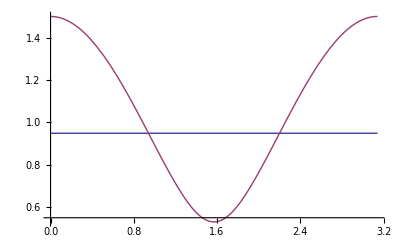

```mathematica
Plot[{Fsqv2Av,√Fsqv2},{θ,0,π}]
```

```mathematica
Minimize[√Fsqv2,θ]
Maximize[√Fsqv2,θ]
```

{3/(4 √2),{θ→π/2}}

{3/2,{θ→0}}

```mathematica
(3./(4 √2))/Fsqv2Av
Fsqv2Av/1.5
```

0.559017

0.632456

### QUALITY FACTOR, ITS NORM-SQUARE and RMS AVERAGE

```mathematica
trigRepl={Sin[2 (ϕ+ϕ1)]->Sin[2ϕ]Cos[2ϕ1]+Cos[2ϕ]Sin[2ϕ1],Sin[2 (ϕ+ϕ2)]->Sin[2ϕ]Cos[2ϕ2]+Cos[2ϕ]Sin[2ϕ2],
Cos[2 (ϕ+ϕ1)]->Cos[2ϕ]Cos[2ϕ1]-Sin[2ϕ]Sin[2ϕ1],Cos[2 (ϕ+ϕ2)]->Cos[2ϕ]Cos[2ϕ2]-Sin[2ϕ]Sin[2ϕ2]};
```

```mathematica
FplusSqSum=Fplus1^2+Fplus2^2+Fplus3^2/.trigRepl/.ϕ1->2π/3/.ϕ2->4π/3//Simplify
FxSqSum=Fx1^2+Fx2^2+Fx3^2/.trigRepl/.ϕ1->2π/3/.ϕ2->4π/3//Simplify
```

1/1024 9 (70+56 Cos[2 θ]+2 Cos[4 θ]-4 Cos[2 (θ-2 ψ)]+Cos[4 (θ-ψ)]+6 Cos[4 ψ]+Cos[4 (θ+ψ)]-4 Cos[2 (θ+2 ψ)])

-1/1024 9 (-70-56 Cos[2 θ]-2 Cos[4 θ]-4 Cos[2 (θ-2 ψ)]+Cos[4 (θ-ψ)]+6 Cos[4 ψ]+Cos[4 (θ+ψ)]-4 Cos[2 (θ+2 ψ)])

```mathematica
FplusSqSumInt=1/(8π)Integrate[(FplusSqSum)Sin[θ]Sin[ι],{θ,0,π},{ψ,0,2π},{ι,0,π}]
FxSqSumInt=1/(8π)Integrate[(FxSqSum)Sin[θ]Sin[ι],{θ,0,π},{ψ,0,2π},{ι,0,π}]
QnormSq=1/2 Integrate[(FplusSqSumInt((1+Cos[i]^2)/2)^2+FxSqSumInt Cos[i]^2)Sin[i],{i,0,-Pi,Pi}]
```

9/20

9/20

9/25

## COSMOLOGICAL REDSHIFT COMPUTATION

```mathematica
(* This data uses 2010 values *)
Clear[z]
RedshiftData=Sort[Import["Redshift.csv","Data"]];
redshift=Interpolation[RedshiftData];
```

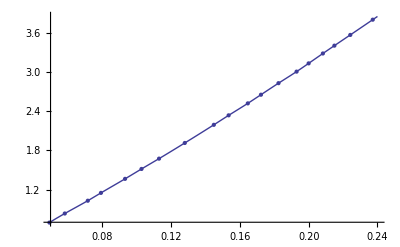

```mathematica
Show[Plot[redshift[z],{z,0.05,0.24}],ListPlot[RedshiftData]]
```

```mathematica
(* Planck 2015 DATA with asro-ph/9905116*)
Pc2LY=3.26156;
GpcScales={1,0.6,0.4,0.2,0.1};
ΩΛ=0.6911;
Ωm=0.3089;
Ωk=1-ΩΛ-Ωm;
Ωr= 9.2364 10^-5;
H0=67.74;
h=H0/100;
Ee[z_]=√(Ωr(1+z)^4+Ωm(1+z)^3+Ωk(1+z)^2+ΩΛ);
dC[z_]:=(clight/10^5)/h NIntegrate[1/Ee[zp],{zp,0,z}];
dM[z_]:=dC[z];
dL[z_]:=(1+z)dM[z];
```

```mathematica
Zs=Table[FindRoot[dL[z0]-1000*GpcScales[[i]],{z0,.2}],{i,1,Length[GpcScales]}]//Quiet
Z1Gpc=Zs[[1,1,2]]
Z600Mpc=Zs[[2,1,2]]
Z400Mpc=Zs[[3,1,2]]
Z200Mpc=Zs[[4,1,2]]
Z100Mpc=Zs[[5,1,2]]
{dL[Z1Gpc],dL[Z600Mpc],dL[Z400Mpc],dL[Z200Mpc],dL[Z100Mpc]}
```

{{z0→0.197981},{z0→0.12425},{z0→0.0850057},{z0→0.0437464},{z0→0.0222204}}

0.197981

0.12425

0.0850057

0.0437464

0.0222204

{1000.,600.,400.,200.,100.}

```mathematica
fISCOshifted=Reverse[GWfreqIsco/(1+{Z1Gpc,Z600Mpc,Z400Mpc,Z200Mpc,Z100Mpc})]
```

{1536.82,1505.12,1447.89,1397.35,1311.34}

## REDSHIFT CORRECTION to STRAIN, τ_insp and SNR

```mathematica
zs=Reverse[{Z1Gpc,Z600Mpc,Z400Mpc,Z200Mpc,Z100Mpc}]
```

{0.0222204,0.0437464,0.0850057,0.12425,0.197981}

```mathematica
HETrs[f_,D_,z_]=Block[{M=2.8 Msun,G=6.67*10^-11,c=clight},Sqrt[QnormSq] A c/D (1+z)^(-1/6) (G Mc/c^3)^(5/6) f^(-7/6)]
```

1703.87/(D f^(7/6) (1+z)^(1/6))

```mathematica
SNRETBrs[fi_,ff_,D_,z_]:=(NIntegrate[4 HETrs[f,D,z]^2/(Snoise[[2]][f])^2,{f,fi,ff}])^(1/2)
SNRETCrs[fi_,ff_,D_,z_]:=(NIntegrate[4 HETrs[f,D,z]^2/(Snoise[[3]][f])^2,{f,fi,ff}])^(1/2)
```

## ET PLOTS with REDSHIFTED SOURCES

### LEGEND

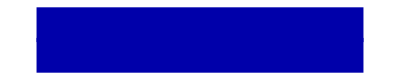
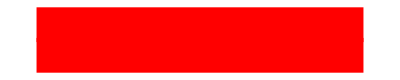
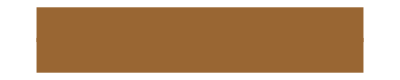
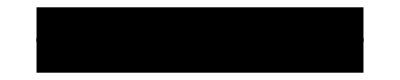

```mathematica
col={Darker[Blue],Red,Brown,Black};
col2={Blue,Darker[Green],Gray};
legmarkers1=MapThread[Graphics[{#1,AbsoluteThickness[3],Line[{{-1,0},{1,0}}],#2}]&,{col,{Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}]}}]
```

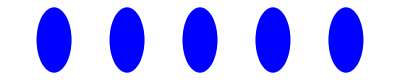
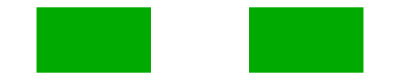
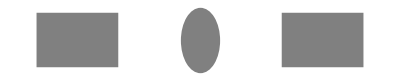

```mathematica
legmarkers2=MapThread[Graphics[{#1,AbsoluteThickness[3],#2}]&,{col2,{{Disk[{1/3,0},0.08],Disk[{0,0},0.08],Disk[{-1/3,0},0.08],Disk[{-2/3,0},0.08],Disk[{2/3,0},0.08]},{Rectangle[{-1,-0.1},{-.3,0.1}],Rectangle[{0.3,-0.1},{1,0.1}]},{Rectangle[{-1,-0.1},{-.5,0.1}],Disk[{0.0,0},0.12],Rectangle[{0.5,-0.1},{1,0.1}]}}}]
```

```mathematica
legmarkers=Flatten[{legmarkers1,legmarkers2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### THE PLOT

```mathematica
fISCOshifted
```

{1536.82,1505.12,1447.89,1397.35,1311.34}

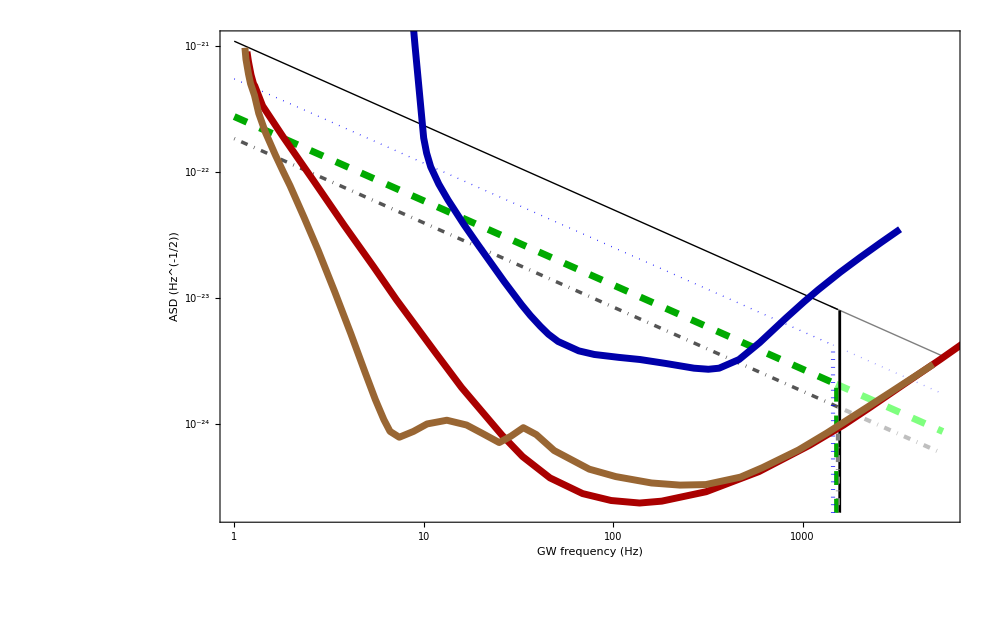

../AA_Letter/Figs/ET_strains_redshifted.pdf

```mathematica
opac=0.5;
ASDPlotsRS=Show[LogLogPlot[{2 √f HETrs[f,100Mpc,zs[[4]]]},{f,1,fISCOshifted[[1]]},PlotRange->{{1,5700},{2 10^-25,1.1 10^-21}},PlotStyle->{Black,Thick}],
LogLogPlot[2 √f HETrs[f,200Mpc,zs[[3]]],{f,1,fISCOshifted[[3]]},PlotStyle->{Blue,Dotted,Thick}],
LogLogPlot[2 √f HETrs[f,400Mpc,zs[[2]]],{f,1,fISCOshifted[[2]]},PlotStyle->{Darker[Green],Thickness[0.005],Dashing[0.01]}],
LogLogPlot[2 √f HETrs[f,600Mpc,zs[[1]]],{f,1,fISCOshifted[[1]]},PlotStyle->{Darker[Gray],Thickness[0.0025],DotDashed}],
LogLogPlot[2 √f HETrs[f,100Mpc,zs[[4]]],{f,fISCOshifted[[4]],5500},PlotStyle->{Black,Opacity[opac],Thick}],
LogLogPlot[2 √f HETrs[f,200Mpc,zs[[3]]],{f,fISCOshifted[[3]],5500},PlotStyle->{Blue,Dotted,Opacity[opac],Thick}],
LogLogPlot[2 √f HETrs[f,400Mpc,zs[[2]]],{f,fISCOshifted[[2]],5500},PlotStyle->{Green,Dashing[0.01],Opacity[opac],Thickness[0.005]}],
LogLogPlot[2 √f HETrs[f,600Mpc,zs[[1]]],{f,fISCOshifted[[1]],5500},PlotStyle->{Gray,Opacity[opac],Thickness[0.003],DotDashed}],
Graphics[{Black,Thickness[0.002],Line[{{Log[GWfreqIsco],Log[2 10^-25]},{Log[GWfreqIsco],Log[ 8 10^-24]}}]}],
Graphics[{Gray,Thickness[0.003],DotDashed,Line[{{Log[fISCOshifted[[1]]],Log[2 10^-25]},{Log[fISCOshifted[[1]]],Log[0.9 10^-24]}}]}],
Graphics[{Darker[Green],Thickness[0.003],Dashing[0.01],Line[{{Log[fISCOshifted[[2]]],Log[2 10^-25]},{Log[fISCOshifted[[2]]],Log[2 10^-24]}}]}],
Graphics[{Blue,Thickness[0.003],Dotted,Line[{{Log[fISCOshifted[[3]]],Log[2 10^-25]},{Log[fISCOshifted[[3]]],Log[4.2 10^-24]}}]}],
ListLogLogPlot[{ALIGO2020Data,ETBData,ETCData},Joined->True,PlotStyle->{{Thickness[0.005],Darker[Blue]},{Thickness[0.005],Darker[Red]},{Thickness[0.005],Brown}},AxesLabel->{"GW freq.",None}],ImageSize->1000,Frame->True,
FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},
GridLines->{{Log[10],Log[5],Log[50],Log[100],Log[500],Log[2],Log[5000]},{Log[10^-24],Log[10^-23],Log[10^-22]}},
FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[ 10^-24],"10^-24"}(*,{Log[5 10^-23],"5x10^-23"}*)},None},{{{Log[2],"2"},{Log[5],"5"},{Log[10],"10"},{Log[50],"50"},{Log[100],"100"},{Log[500],"500"},{Log[5000],"5000"},(*{Log[1000],"1000"},*){Log[GWfreqIsco],"f_ISCO"}},None}},FrameTicksStyle->24,
Epilog->Inset[Framed[Column[{PointLegend[{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},{Style["A-LIGO",TextSize],Style["ET-B",TextSize],Style["ET-C",TextSize],Style["BNS at 100 Mpc",TextSize],Style["BNS at 200 Mpc",TextSize],Style["BNS at 400 Mpc",TextSize],Style["BNS at 600 Mpc",TextSize]},LegendMarkers->legmarkers,LegendMarkerSize->{30,10}]}],(*FrameStyle->Directive[Black,AbsoluteThickness[5]],*)RoundingRadius->5,Background->White],Scaled[{0.87,0.8}]]]
(*Export["../AA_Letter/Figs/ET_strains_redshifted.pdf",ASDPlotsRS]*)
```

## ET-B, ET-C Advance Warning Times and SNRs 3.5PN calculation uses x -> x (1+z)^(2/3) and Θ -> (1+z)^-1Θ

```mathematica
M=2.8 Msun
```

5.5692×10^30

### ET-B, ET-C entry frequencies f_0 for 4 sources

```mathematica
ETf0RootFinderRS[D_,fB_,fC_,z_]:={2 √fB HETrs[fB,D,z]-Snoise[[2]][fB],2 √fC HETrs[fC,D,z]-Snoise[[3]][fC]}
```

```mathematica
f0ETrs={FindRoot[ETf0RootFinderRS[100Mpc,f1,f2,zs[[1]]],{{f1,1},{f2,1}}][[All,2]],
FindRoot[ETf0RootFinderRS[200Mpc,f1,f2,zs[[2]]],{{f1,1},{f2,1}}][[All,2]],FindRoot[ETf0RootFinderRS[400Mpc,f1,f2,zs[[3]]],{{f1,1},{f2,1}}][[All,2]],
FindRoot[ETf0RootFinderRS[600Mpc,f1,f2,zs[[4]]],{{f1,1},{f2,1}}][[All,2]],FindRoot[ETf0RootFinderRS[1000Mpc,f1,f2,zs[[4]]],{{f1,1},{f2,1}}][[All,2]]}//Quiet
```

{{1.15173,1.13483},{1.30064,1.2336},{1.92124,1.45212},{2.52253,1.68966},{3.59707,2.09517}}

```mathematica
f0B=f0ETrs[[All,1]]
f0C=f0ETrs[[All,2]]
```

{1.15173,1.30064,1.92124,2.52253,3.59707}

{1.13483,1.2336,1.45212,1.68966,2.09517}

### D = 100 Mpc

```mathematica
(* ET-B *)
DL=100Mpc;
j=1;
(*fbar=6.7237;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]*)

(* ET-C *)
fbar=4.09853(*3.26919 (*ρ=15 value*) *);
Print["SNR_detection = ", SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

SNR_detection = 30.

τ_insp = 10523.9(3.5PN), 10524.5(2PN) 10432.3(0 PN)  seconds

τ_insp = 2.92331 hours(3.5PN),

ρ_tot = 365.544

### D = 200 Mpc

```mathematica
(* ET-B *)
DL=200Mpc;
j=2;
(*fbar=11.21037;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]*)

(* ET-C *)
fbar=5.0509 (* SNR=30 value*);
Print["SNR_detection = ",SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

SNR_detection = 30.

τ_insp = 5829.08(3.5PN), 5829.52(2PN) 5771.93(0 PN)  seconds

τ_insp = 1.61919 hours(3.5PN),

ρ_tot = 182.137

### D = 400 Mpc

```mathematica
(* ET-B *)
DL=400Mpc;
j=3;
(*fbar=18.2234;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]*)

(* ET-C *)
fbar=6.22662(*5.06068 (*SNR=15 value*)*);
SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), or ",Tinsp3p5PN/60," minutes"]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

29.9999

τ_insp = 3131.47(3.5PN), 3131.82(2PN) 3096.73(0 PN)  seconds

τ_insp = 0.869853 hours(3.5PN), or 52.1912 minutes

ρ_tot = 90.4805

### D = 600 Mpc

```mathematica
(* ET-B *)
DL=600Mpc;
j=4;
fbar=7.2875;
SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN) or ",Tinsp3p5PN/60," minutes"]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

29.9999

τ_insp = 1942.22(3.5PN), 1942.51(2PN) 1918.59(0 PN)  seconds

τ_insp = 0.539504 hours(3.5PN), or 32.3703 minutes

ρ_tot = 59.9626

### D = 1000 Mpc

```mathematica
(* ET-B *)
DL=1000Mpc;
j=5;
(*fbar=41.3537;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
*)
(* ET-C *)
fbar=6.75534;
SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]
Print["SNR_detection = ",Ceiling[SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN)  or ",Tinsp3p5PN/60," minutes"]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

14.9997

SNR_detection = 15

τ_insp = 2138.48(3.5PN), 2138.8(2PN) 2112.61(0 PN)  seconds

τ_insp = 0.594022 hours(3.5PN)  or 35.6413 minutes

ρ_tot = 35.5958

## ET-B, ET-C Horizon Distance Computation for T_AW= 1 hour

### ET-B

```mathematica
dtest=86.87;
ztest=FindRoot[dL[z0]-dtest,{z0,.2}][[1,2]]//Quiet;
ftest=FindRoot[Tinsp0PN[f1,(1+ztest)Mc] -3600,{f1,20}][[1,2]];
fintest=FindRoot[2 √fC HETrs[fC,dtest Mpc,ztest]-Snoise[[2]][fC],{fC,1}][[1,2]]//Quiet;
SNRETBrs[fintest,ftest,dtest Mpc,ztest]
(dtest/1000.)^3{1540-1220,1540,1540+3200};
(dtest/1000.)^3{1220,3200};
SNRETCrs[fintest,GWfreqIsco/(1+ztest),dtest Mpc,ztest]
Print["Time it takes to accumulate ρ=15:\t", (Tinsp0PN[fintest,(1+ztest)Mc] -Tinsp0PN[ftest,(1+ztest)Mc] )/3600/24, " days"]
```

15.0106

420.993

Time it takes to accumulate ρ=15:	3.75169 days

### ET-C

```mathematica
dtest=613;
ztest=FindRoot[dL[z0]-dtest,{z0,.2}][[1,2]]//Quiet;
ftest=FindRoot[Tinsp0PN[f1,(1+ztest)Mc] -3600,{f1,20}][[1,2]];
fintest=FindRoot[2 √fC HETrs[fC,dtest Mpc,ztest]-Snoise[[3]][fC],{fC,1}][[1,2]]//Quiet;
SNRETCrs[fintest,ftest,dtest Mpc,ztest]
Print["Time it takes to accumulate ρ=15:\t", (Tinsp0PN[fintest,(1+ztest)Mc] -Tinsp0PN[ftest,(1+ztest)Mc] )/3600/24, " days"]
```

15.0087

Time it takes to accumulate ρ=15:	1.02118 days

```mathematica
(* EVENT RATES within horizon distance *)
```

```mathematica
(dtest/1000.)^3{1540-1220,1540,1540+3200}
(dtest/1000.)^3{1220,3200}
```

{73.7108,354.733,1091.84}

{281.023,737.108}

```mathematica
(* Total SNR at horizon distance *)
SNRETCrs[fintest,GWfreqIsco/(1+ztest),dtest Mpc,ztest]
```

58.6692

## EVENT RATE vs. D PLOT

```mathematica
R={1540,1540+3200,1540-1220};
```

```mathematica
Rdensity[D_]= R*(D/1000)^3;
```

```mathematica
Rdensity[D][[3]]
```

D^3/3125000

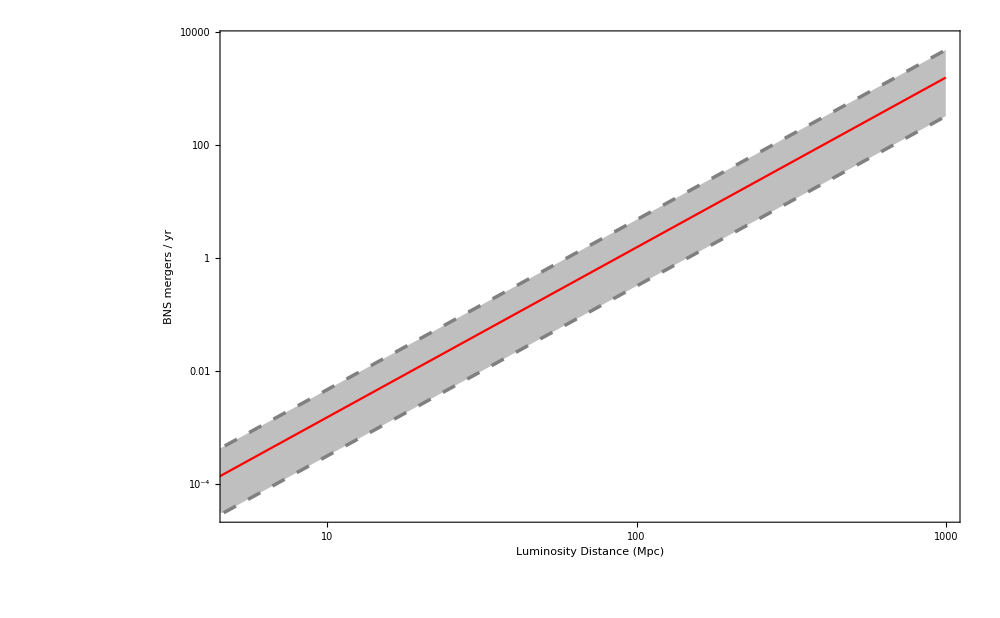

```mathematica
RvsDPlot=LogLogPlot[{Rdensity[D][[1]],Rdensity[D][[2]],Rdensity[D][[3]]},{D,1,1000},PlotStyle->{Red,{Gray,Dashing[0.01],Thickness[0.0025]},{Gray,Dashing[0.01],Thickness[0.0025]}},Filling->{2->{3}},FillingStyle->Directive[Gray,Opacity[0.5]],PlotRange->{{5,1000},{10^-4.5,7000}},Frame->True,FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["Luminosity   Distance (Mpc)",24],Style["BNS mergers / yr",24]},
FrameTicks->{{{{10^-1,"10^-1"},{10^-3,"10^-3"},{1,"1"},{ 10^2,"100"},{10,"10"},{3000,"3000"},{1000,"1000"}},None},{{{10,"10"},{50,"50"},{100,"100"},{500,"500"},{1000,"1000"}},None}},FrameTicksStyle->24,
GridLines->{{10,50,100,500,{613,Directive[Thickness[0.0025],Darker[Green]]},{87,Directive[Thickness[0.0025],Darker[Blue]]}},{0.1,0.001,1,10,100,{1540,Directive[Thick,Red]},{4740,Directive[Thickness[0.0025],Dashing[0.01],Darker[Gray]]},{320,Directive[Thickness[0.0025],Dashing[0.01],Darker[Gray]]}}},
ImageSize->1000]
(*Export["../AA_Letter/Figs/EventRate_vs_Distance.pdf",RvsDPlot]*)
```

## ET-C EVENT RATES per 50Mpc BINS

```mathematica
Bins=50.*Range[1,12]
```

{50.,100.,150.,200.,250.,300.,350.,400.,450.,500.,550.,600.}

```mathematica
binStrings=Table[{i,ToString[IntegerPart[Bins[[i]]]]<>"-"<>ToString[IntegerPart[Bins[[i+1]]]]},{i,1,Length[Bins]-1}]
```

{{1,50-100},{2,100-150},{3,150-200},{4,200-250},{5,250-300},{6,300-350},{7,350-400},{8,400-450},{9,450-500},{10,500-550},{11,550-600}}

```mathematica
RateBins=Table[Rdensity[Bins[[i+1]]][[k]]-Rdensity[Bins[[i]]][[k]],{k,1,Length[R]},{i,1,Length[Bins]-1}];
AvRateBins=%[[1]]
LowerRateBins=RateBins[[3]]
UpperRateBins=RateBins[[2]]
```

{1.3475,3.6575,7.1225,11.7425,17.5175,24.4475,32.5325,41.7725,52.1675,63.7175,76.4225}

{0.28,0.76,1.48,2.44,3.64,5.08,6.76,8.68,10.84,13.24,15.88}

{4.1475,11.2575,21.9225,36.1425,53.9175,75.2475,100.133,128.573,160.568,196.118,235.222}

### Making the Log Bar Chart

```mathematica
stackedBars=Table[Log[{LowerRateBins[[i]],AvRateBins[[i]],UpperRateBins[[i]]}],{i,1,Length[AvRateBins]}]
```

{{-1.27297,0.298251,1.42251},{-0.274437,1.29678,2.42103},{0.392042,1.96326,3.08751},{0.891998,2.46321,3.58747},{1.29198,2.8632,3.98746},{1.62531,3.19653,4.32078},{1.91102,3.48224,4.60649},{2.16102,3.73224,4.85649},{2.38324,3.95446,5.07871},{2.58324,4.15446,5.27871},{2.76506,4.33628,5.46053}}

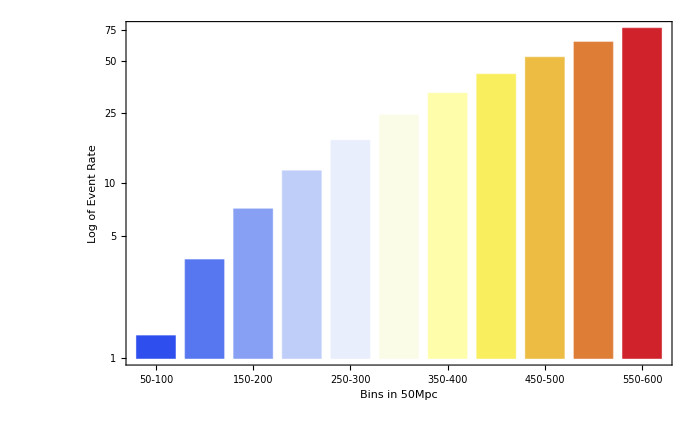

../AA_Letter/Figs/EventRate_per_50Mpc.pdf

```mathematica
Ratein50MpcBins=BarChart[
stackedBars[[All,2]],BarSpacing->Medium,BarOrigin->Bottom
,ChartStyle->{"TemperatureMap"}
,PlotRange->{{0,Automatic},Automatic}
,Frame->True,FrameLabel->{Style["Bins in 50Mpc",20],Style["Log of Event Rate",20]},(*FrameTicksStyle->24,*)FrameStyle->Directive[Black,12,AbsoluteThickness[3]]
,FrameTicks->{{{{Log[1],"1"},{Log[5],"5"},{Log[10],"10"},{Log[50],"50"},{Log[25],"25"},{Log[75],"75"}},None},{binStrings,None}}
,GridLines->{None,{Log[5],Log[10],Log[25],Log[50],Log[75]}}
,ImageSize->700
(*,ChartLabels->Placed[binStrings,Bottom]*)
]
Export["../AA_Letter/Figs/EventRate_per_50Mpc.pdf",Ratein50MpcBins]
```

## ET-C EVENT RATES per redshift Bins of width 0.05

```mathematica
redshifts=0.01*Range[1,12]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12}

```mathematica
ZsandDs=Table[{redshifts[[i]],dL[redshifts[[i]]]},{i,1,Length[redshifts]}]
```

{{0.01,44.593},{0.02,89.8587},{0.03,135.789},{0.04,182.378},{0.05,229.617},{0.06,277.5},{0.07,326.018},{0.08,375.165},{0.09,424.933},{0.1,475.316},{0.11,526.305},{0.12,577.895}}

```mathematica
RinRedshiftBins=Table[Rdensity[ZsandDs[[i+1,2]]][[k]]-Rdensity[ZsandDs[[i,2]]][[k]],{k,1,Length[R]},{i,1,Length[ZsandDs]-1}];
AvRateBins=RinRedshiftBins[[1]]
LowerRateBins=RinRedshiftBins[[3]]
UpperRateBins=RinRedshiftBins[[2]]
```

{0.98082,2.73846,5.48614,9.30182,14.2647,20.4551,27.9545,36.8452,47.2107,59.1353,72.7038}

{0.203807,0.569031,1.13998,1.93285,2.96409,4.25041,5.80872,7.65615,9.81003,12.2878,15.1073}

{3.01889,8.42877,16.8859,28.6303,43.9056,62.9592,86.0417,113.407,145.311,182.014,223.777}

```mathematica
redshiftBinStrings=Join[{{1,"(0-1)Δz"}},Table[{i,"("<>ToString[i]<>"-"<>ToString[i+1]<>")""Δz"},{i,2,Length[AvRateBins]}]]
```

{{1,(0-1)Δz},{2,(2-3) Δz},{3,(3-4) Δz},{4,(4-5) Δz},{5,(5-6) Δz},{6,(6-7) Δz},{7,(7-8) Δz},{8,(8-9) Δz},{9,(9-10) Δz},{10,(10-11) Δz},{11,(11-12) Δz}}

```mathematica
Δz=0.01;
```

```mathematica
redshiftBinStrings=Join[{{1,"0-0.01"}},Table[{i,ToString[Δz*i]<>"-"<>ToString[Δz(i+1)]},{i,2,Length[AvRateBins]}]]
```

{{1,0-0.01},{2,0.02-0.03},{3,0.03-0.04},{4,0.04-0.05},{5,0.05-0.06},{6,0.06-0.07},{7,0.07-0.08},{8,0.08-0.09},{9,0.09-0.1},{10,0.1-0.11},{11,0.11-0.12}}

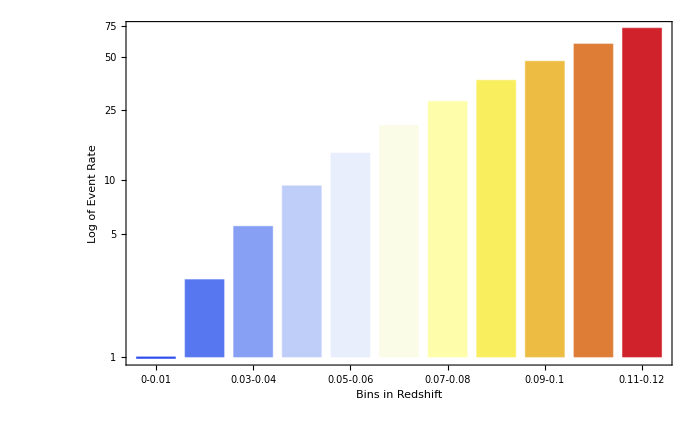

../AA_Letter/Figs/EventRate_per_RedshiftBin.pdf

```mathematica
RateinRedshiftBins=BarChart[
Log[AvRateBins],BarSpacing->Medium,BarOrigin->Bottom
,ChartStyle->{"TemperatureMap"}
,PlotRange->{{0,Automatic},Automatic}
,Frame->True,FrameLabel->{Style["Bins in Redshift",20],Style["Log of Event Rate",20]},FrameStyle->Directive[Black,10,AbsoluteThickness[3]]
,FrameTicks->{{{{Log[1],"1"},{Log[5],"5"},{Log[10],"10"},{Log[50],"50"},{Log[25],"25"},{Log[75],"75"}},None},{redshiftBinStrings,None}}
,GridLines->{None,{Log[5],Log[10],Log[25],Log[50],Log[75]}}
,ImageSize->700
(*,ChartLabels->Placed[binStrings,Bottom]*)
]
Export["../AA_Letter/Figs/EventRate_per_RedshiftBin.pdf",RateinRedshiftBins]
```